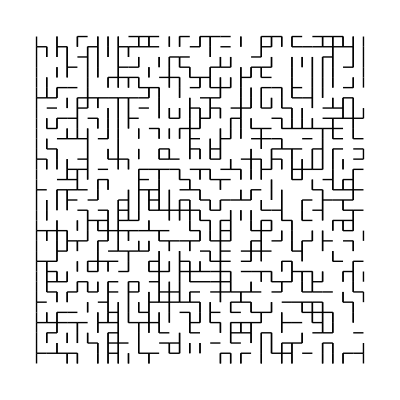

```mathematica
d = 32; 
width = height = d; 
EX = Table[{i, j} <-> {i + 1, j}, {i, width}, {j, width}]; 
EY = Table[{i, j} <-> {i, j + 1}, {i, width}, {j, width}]; 
p = 0.5; 
q = 0.6; 
Ex = RandomChoice[{p, 1 - p} -> {#, {}}]& /@ Flatten @ EX; 
Ex = Cases[Except[{}]][Ex]; 
Ey = RandomChoice[{q, 1 - q} -> {#, {}}]& /@ Flatten @ EY; 
Ey = Cases[Except[{}]][Ey]; 
g = Graph[Join[Ex, Ey]]; 
walls =
    Table[
        {
            If[EdgeQ[g, {i, j} <-> {i + 1, j}],
                {}
                ,
                {Line[{{i + .5, j + .5}, {i + .5, j - .5}}]}
            ]
            ,
            If[EdgeQ[g, {i, j} <-> {i - 1, j}],
                {}
                ,
                {Line[{{i - .5, j + .5}, {i - .5, j - .5}}]}
            ]
            ,
            If[EdgeQ[g, {i, j} <-> {i, j + 1}],
                {}
                ,
                {Line[{{i - .5, j + .5}, {i + .5, j + .5}}]}
            ]
        }
        ,
        {i, width}
        ,
        {j, height}
    ]; 
Graphics[walls]
```

```mathematica
Clear[start]; 
start = {Floor[width / 2], height}; 
Clear[frontier]; 
frontier = {start}; 
Clear[backTrack]; 
backTrack[v_] = {}; 
Clear[visited]; 
visited[v_] :=
    False; 
Clear[frontierTime]; 
fontierTime[v_] :=
    1000; 
Clear[groundNodes]; 
groundNodes = {}; 
Clear[time]; 
time = 1; 
Clear[bestNodes]; 
bestNodes = {start}; 
Clear[newFrontier]; 
G = Graphics[walls]; 
While[
    And[Length[groundNodes] == 0, Length[frontier] > 0]
    ,
    newFrontier = {};
    Do[
        visited[v] = True;
        Do[
            AppendTo[newFrontier, u];
            frontierTime[u] = time;
            backTrack[u] = v;
            
            ,
            {u, Select[VertexList[NeighborhoodGraph[g, v]], Not[visited[
                #]]&]}
        ];
        
        ,
        {v, frontier}
    ];
    frontier = Union[newFrontier];
    groundNodes = Select[frontier, Last[#] == 1&];
    AppendTo[
        bestNodes
        ,
        If[Length[frontier] == 0,
            {}
            ,
            SortBy[frontier, Last][[1]]
        ]
    ];
    time += 1;
    
]; 
end = groundNodes[[1]]; 
path = NestWhileList[backTrack, end, # ≠ start&]; 
AppendTo[path, start]; 
Graphics[{walls, Thick, Pink, Line[path]}]
```

-Graphics-